arxiv : 2112.09699

Reproducing Fig. 7 in arxiv : 2112.09699

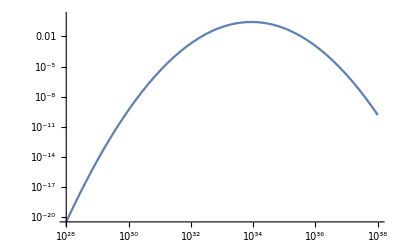

```mathematica
LogLogPlot[L Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[8.8 10^33],sL->0.62},{L,10^28,10^38}]
```

use the luminosity of the galactic center excess to determine the number of MSP

```mathematica
-Graphics--Graphics-
```

from Table 1 of arXiv:1512.04966

```mathematica
13750 Integrate[L^1 Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[4.7 10^32],sL->1.75},{L,10^29,10^60}]
5187.2 Integrate[L^1 Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[4.7 10^32],sL->2.25},{L,10^29,10^60}]
6212 Integrate[L^1 Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[1.8 10^33],sL->1.4},{L,10^29,10^80}]
2024.4 Integrate[L^1 Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[5.5 10^33],sL->1.4},{L,10^29,10^80}]
```

2.16887×10^40

1.64229×10^42

2.01854×10^39

2.00998×10^39

Fig.3 of arxiv : 2112.09699

L = F/(1.11 * 10^-46 cm^-2) ~ 10^37 erg/s

```mathematica
Lumin = Integrate[L^1 Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[8.8 10^33],sL->0.62},{L,10^29,10^60}] (*GLC*)
10^37/Lumin
```

2.43803×10^34

410.167

```mathematica
410/670.
```

0.61194

```mathematica
Lumin = Integrate[L^1 Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[1.3 10^32],sL->0.7},{L,10^29,10^60}] (*GCE*)
10^37/Lumin
```

4.76515×10^32

20985.7

```mathematica
20986/35000.
```

0.5996

Constrain ourselves to the parameter space where 1) less than 20% of MSPs (responsible for the GeV excess) are detectable by Fermi; or 2) the detectable MSPs contribute less than 20% of the luminosity to explain the GeV excess. This means that outside this parameter space, a handful of bright and observable pulsars are responsible to explain the GeV excess. This scenario seems to be disfavored by astro observations.

```mathematica
LS={{31.315974359359288,1.0007846214201648},{31.546680077462362,0.9563184533954171},{31.83233002567067,0.9001472772993588},{32.1400777625989,0.8299043662252635},{32.41479891312507,0.7713793258687109},{32.59074054613965,0.7245335682910046},{32.83270532778887,0.6565995022155908},{33.041733595544414,0.5933410080455853},{33.338912824823986,0.4925750374624571},{33.50419587768154,0.42224851918785256},{33.64741116598863,0.36364630295390676},{33.823743113206135,0.2862839171902837},{33.95614970050892,0.2159381049463307},{34.05570984642638,0.14322556579565116},{34.10038581057752,0.07752316884152566},{34.1232642277033,0.0024181774916554044}};
```

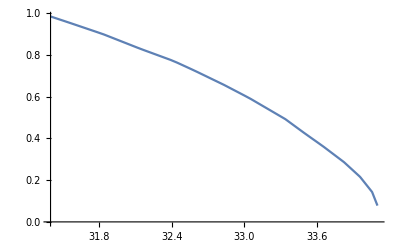

```mathematica
bound=Interpolation[LS,InterpolationOrder->1];
Plot[bound[x],{x,31.4,34.1}]
```

```mathematica
NMPS={};
For[i=31.4,i≤34.1,i=i+0.03,For[j=0.05,j≤1,j=j+0.04,{If[j<bound[i],{Lumin = Integrate[L^1 Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[10^i],sL->j},{L,10^29,10^60}],NMPS=AppendTo[NMPS,{i,j,10^37/Lumin}]}]}]]
```

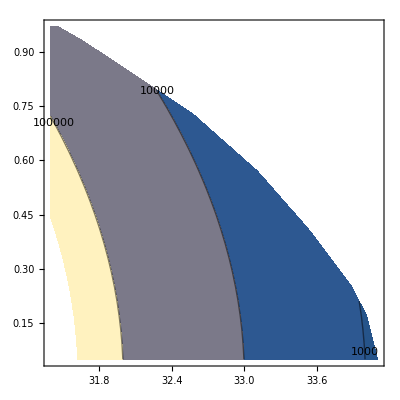

```mathematica
ListContourPlot[NMPS,Contours->{10^3,10^4,10^5},ContourLabels->All]
```

```mathematica
NMPSros={};
count=0;
For[i=31.4,i≤34.1,i=i+0.03,For[j=0.05,j≤1,j=j+0.04,{If[j<bound[i],{count=count+1,ProbRos= Integrate[Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[10^i],sL->j},{L,10^34,10^60}],NMPSros=AppendTo[NMPSros,{i,j,ProbRos NMPS[[count,-1]]}]}]}]]
```

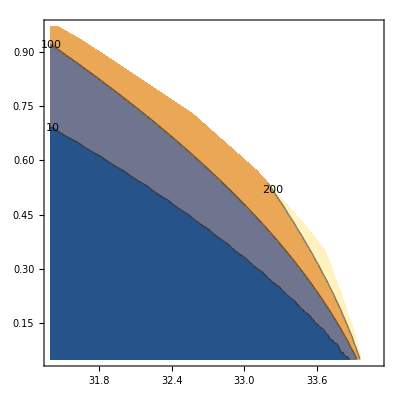

```mathematica
ListContourPlot[NMPSros,Contours->{10^1,10^2,200},ContourLabels->All]
```

There  seems to be something wrong with Gopi’s paper.

```mathematica
LS2lower={{31.79833628577168,2.623995407577497},{31.90785652975875,2.5000690989496963},{32.37820735248461,1.954745503252966},{32.73246342933324,1.5706350725007445},{32.89964753364866,1.4531668580176045},{33.0729130522125,1.4103520857252203},{33.17522873787826,1.4667474592847727},{33.27738006099676,1.5604562656801464},{33.33441386489398,1.7099491856954547},{33.35331555782822,1.7846557809244379}};
LS2upper={{33.35331555782822,1.7846557809244379},{33.14747886115017,1.9454968746013521},{32.851681063608304,2.1557171407917677},{32.55599284109794,2.341061785091636},{32.30544953156674,2.4644034102989325},{32.13845718355644,2.5383392864736147},{31.97795715616268,2.5936450227495005},{31.81121135197326,2.6116107496704513}};
```

InterpolatingFunction::dmval: Input value {31.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

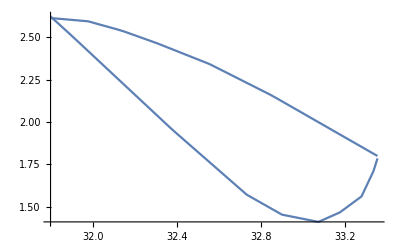

```mathematica
bound2lower=Interpolation[LS2lower,InterpolationOrder->1];
bound2upper=Interpolation[LS2upper,InterpolationOrder->1];
Show[{Plot[bound2lower[x],{x,31.8,33.35331555782822}], Plot[bound2upper[x],{x,31.8,33.35331555782822}]}]
```

```mathematica
NMPS2={};
For[i=31.8,i≤33.35,i=i+0.1,For[j=1.41,j≤2.6,j=j+0.05,{If[bound2lower[i]<j<bound2upper[i],{Lumin = Integrate[L^1 Log10[E]/(sL √(2π)L)Exp[-(Log10[L]-Log10L0)^2/(2 sL^2)]/.{Log10L0->Log10[10^i],sL->j},{L,10^29,10^60}],NMPS2=AppendTo[NMPS2,{i,j,10^37/Lumin}]}]}]]
```

InterpolatingFunction::dmval: Input value {31.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

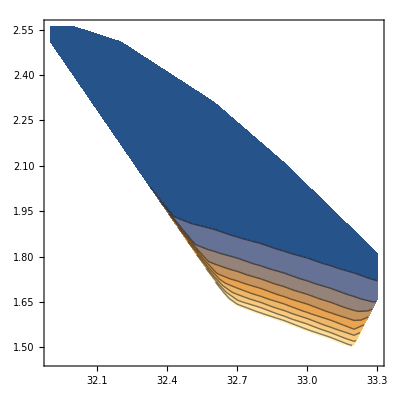

```mathematica
ListContourPlot[NMPS2]
```